## LieARTCharacters

### Setup

```mathematica
SetDirectory@NotebookDirectory[];
<<LieARTCharacters`
```

### LieART extension/modding

#### Rank

Rank now works with ProductAlgebra, ProductIrrep and ProductWeight, returning the rank of the underlying algebra.

```mathematica
Rank@ProductAlgebra[A2,A2,A2]
```

6

```mathematica
Rank@ProductWeight[Weight[A2][1,0],Weight[A2][1,1],Weight[A2][1,2]]
```

6

#### Algebra

Algebra gives the correct result for ProductIrrep, ProductWeight, IrrepPlus and IrrepTimes returning the algebra we are working with.

```mathematica
Algebra@ProductIrrep[Irrep[A1][1],Irrep[D2][1,0],Irrep[B2][1,1]]
```

A_1×D_2×B_2

```mathematica
IrrepPlus[
ProductIrrep[Irrep[A2][1,0],Irrep[A2][1,0],Irrep[A2][0,1]],
IrrepTimes[3,ProductIrrep[Irrep[A2][0,1],Irrep[A2][1,0],Irrep[A2][0,1]]]
]
%//Algebra
```

((10),(10),(01))+3((01),(10),(01))

A_2×A_2×A_2

```mathematica
Algebra@IrrepPlus[Irrep[D2][1,0],Irrep[A2][0,1]]
```

Algebra::irrplusdiff: IrrepPlus contains irreps of different algebras {A_2,D_2}.

Algebra[(10)+(01)]

#### Irrep / ProductIrrep and Weight / Product Weight

Irrep/Weight of ProductAlgebra automatically expends to ProductIrrep/ProductWeight.

```mathematica
Irrep[ProductAlgebra[A1,A2,A1]][1,1,0,2]
%//FullForm
```

((1),(10),(2))

ProductIrrep[Irrep[A][1],Irrep[A][1,0],Irrep[A][2]]

#### WeylDimensionFormula

```mathematica
WeylDimensionFormula[ProductAlgebra[A2,A2,A2]][x1,x2,y1,y2,z1,z2]
WeylDimensionFormula[A2][x1,x2]WeylDimensionFormula[A2][y1,y2]WeylDimensionFormula[A2][z1,z2]
%==%%
```

1/8 (1+x1) (1+x2) (2+x1+x2) (1+y1) (1+y2) (2+y1+y2) (1+z1) (1+z2) (2+z1+z2)

1/8 (1+x1) (1+x2) (2+x1+x2) (1+y1) (1+y2) (2+y1+y2) (1+z1) (1+z2) (2+z1+z2)

True

### Computation of characters

χ[irrep] computes the “pure function” using WeightSystem[irrep] of LieART and saves it in the current session memory since the computation of the weights can be time consuming.
The variable $SaveCharacterDefinitions can be modified if memory is a concern.

```mathematica
χ[Irrep[E6][1,0,0,0,0,0]]
```

#1+#2/#1+#3/#2+#2/#4+#3/(#1 #4)+(#1 #3)/(#2 #4)+#4/#3+1/#5+#4/(#1 #5)+(#1 #4)/(#2 #5)+(#2 #4)/(#3 #5)+#5/#1+(#1 #5)/#2+(#2 #5)/#3+#5/#4+#1/#6+#2/(#1 #6)+#3/(#2 #6)+#4/#6+#3/(#5 #6)+(#3 #5)/(#4 #6)+#6/#2+(#1 #6)/#3+(#2 #6)/(#1 #3)+(#4 #6)/#3+#6/#5+(#5 #6)/#4&

```mathematica
χ[Irrep[E6][1,0,0,0,0,0]][z1,z2,z3,z4,z5,z6]
```

z1+z2/z1+z3/z2+z2/z4+z3/(z1 z4)+(z1 z3)/(z2 z4)+z4/z3+1/z5+z4/(z1 z5)+(z1 z4)/(z2 z5)+(z2 z4)/(z3 z5)+z5/z1+(z1 z5)/z2+(z2 z5)/z3+z5/z4+z1/z6+z2/(z1 z6)+z3/(z2 z6)+z4/z6+z3/(z5 z6)+(z3 z5)/(z4 z6)+z6/z2+(z1 z6)/z3+(z2 z6)/(z1 z3)+(z4 z6)/z3+z6/z5+(z5 z6)/z4

By default, Algebra[A][n] algebra family is used if a list of Dynkin labels is provided.

```mathematica
χ[{1,0,0}]
```

#1+#2/#1+1/#3+#3/#2&

There are different ways of calling χ. Additionally, ProductAlgebra also is compatible.

```mathematica
χ[E6,{1,0,0,0,0,0}]==χ[Irrep[E6][1,0,0,0,0,0]]
```

True

```mathematica
χ[ProductAlgebra[A2,B2,C2],{{1,0},{0,1},{1,1}}]==χ[ProductIrrep[Irrep[A][1,0],Irrep[B][0,1],Irrep[C][1,1]]]==χ[{A2,B2,C2},{{1,0},{0,1},{1,1}}]
```

True

More importantly, IrrepPlus and IrrepTimes automatically expand and give the correct result in terms of character sum and multiplication.

```mathematica
χ[IrrepPlus[
ProductIrrep[Irrep[A2][1,0],Irrep[A2][1,0],Irrep[A2][0,1]],
IrrepTimes[3,ProductIrrep[Irrep[A2][0,1],Irrep[A2][1,0],Irrep[A2][0,1]]]
]]
```

3 (1/#1+#1/#2+#2) (#3+1/#4+#4/#3) (1/#5+#5/#6+#6)+(#1+1/#2+#2/#1) (#3+1/#4+#4/#3) (1/#5+#5/#6+#6)&

### Character sum decomposition

Assume a random ansatz for a product algebra of three A_2 algebras

```mathematica
g=ProductAlgebra[A2,A2,A2];
irrepSampleList=RandomInteger[{0,3},{8,Rank[g]}]
irrepList=Irrep[g]@@@irrepSampleList
```

{{0,3,0,2,0,1},{3,0,2,3,1,1},{1,2,3,2,0,0},{0,2,2,1,3,2},{1,1,3,3,3,2},{2,3,0,0,1,0},{1,1,1,2,2,3},{1,1,1,2,1,0}}

{((03),(02),(01)),((30),(23),(11)),((12),(32),(00)),((02),(21),(32)),((11),(33),(32)),((23),(00),(10)),((11),(12),(23)),((11),(12),(10))}

```mathematica
irrepAnsatz=IrrepPlus@@MapIndexed[
Function[{rep,i},IrrepTimes[a[First@i],rep]],
irrepList
]
```

a[1]((03),(02),(01))+a[2]((30),(23),(11))+a[3]((12),(32),(00))+a[4]((02),(21),(32))+a[5]((11),(33),(32))+a[6]((23),(00),(10))+a[7]((11),(12),(23))+a[8]((11),(12),(10))

```mathematica
ansatz=Expand[
χ[irrepAnsatz][z1,z2,z3,z4,z5,z6]
]
```

```mathematica
decomp=CharacterDecomposition[g][ansatz,{z1,z2,z3,z4,z5,z6}]
```

<|((02),(21),(32))→a[4],((03),(02),(01))→a[1],((23),(00),(10))→a[6],((30),(23),(11))→a[2],((11),(12),(10))→a[8],((11),(12),(23))→a[7],((11),(33),(32))→a[5],((12),(32),(00))→a[3]|>

```mathematica
Total@KeyValueMap[#2 χ[#1][z1,z2,z3,z4,z5,z6]&,decomp]-ansatz//ExpandAll
```

0

### Highest weights

For the computation of the decomposition it is necessary to order the dominant weights and extract the highest weights from a given expression.

```mathematica
g=B3;
irrepSampleList=RandomInteger[{0,2},{3,Rank[g]}]
irrepList=Irrep[g]@@@irrepSampleList;
weightList=Flatten[WeightSystem/@irrepList];
```

{{0,1,2},{1,1,1},{2,2,0}}

The highest weights can be computed as the  root nodes of a relation graph. We compute the well-known weak ordering using DominantWeightOrder

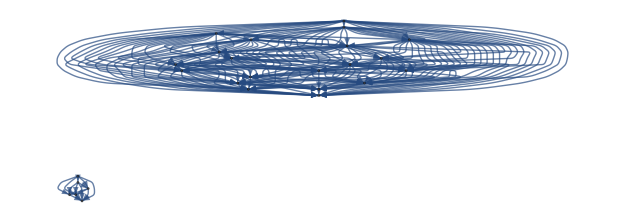

```mathematica
RelationGraph[DominantWeightOrder[#1,#2]>0 &,Union@DominantWeights@weightList]
```

For a list of weights we use HighestWeights

```mathematica
HighestWeights[weightList]
```

{(1, 1, 1),(2, 2, 0)}

For an expression which is given by a sum of characters we can use HighestWeightsFrom

```mathematica
testCharacter=Sum[χ[ir][z1,z2,z3],{ir,irrepList}];
```

```mathematica
HighestWeightsFrom[g][testCharacter,{z1,z2,z3}]
```

{(2, 2, 0),(1, 1, 1)}